```mathematica
r 1/(Cos[ArcTan[t-(r-2G μ Log[1+r/(2G μ)])]]Cos[ArcTan[t+(r-2G μ Log[1+r/(2G μ)])]])
Limit[%,r->Infinity]
```

r √(1+(r-t-2 G μ Log[1+r/(2 G μ)])^2) √(1+(r+t-2 G μ Log[1+r/(2 G μ)])^2)

∞

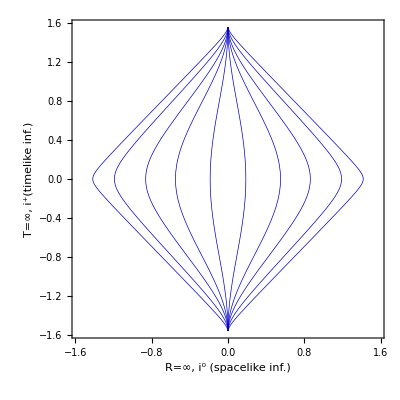

```mathematica
Clear[p,t,r]
μ=1;G=1;c=0;
rconst[r_]:=Table[1/2{
ArcTan[t-(r-2G μ Log[1+r/(2G μ)])]-ArcTan[t+(r-2G μ Log[1+r/(2G μ)])],
ArcTan[t-(r-2G μ Log[1+r/(2G μ)])]+ArcTan[t+(r-2G μ Log[1+r/(2G μ)])]},{t,-100,100,0.1}];
rconstP=Table[rconst[k],{k,{1,2,3,5,10}}];
rconst[r_]:=Table[1/2{
-(ArcTan[t-(r-2G μ Log[1+r/(2G μ)])]-ArcTan[t+(r-2G μ Log[1+r/(2G μ)])]),
ArcTan[t-(r-2G μ Log[1+r/(2G μ)])]+ArcTan[t+(r-2G μ Log[1+r/(2G μ)])]},{t,-100,100,0.1}];
rconstM=Table[rconst[k],{k,{1,2,3,5,10}}];
PD1=ListLinePlot[Flatten[{rconstP,rconstM},1],PlotRange->{{-Pi/2,Pi/2},{-Pi/2,Pi/2}},AspectRatio->1,
Frame->True,
AxesLabel->{"R=∞, i^0 (spacelike inf.) ","T=∞, i^+(timelike inf.)"},
PlotStyle->{{RGBColor[0.0,0,0.8],AbsoluteThickness[0.5]}},
PlotLegends->Automatic]
```

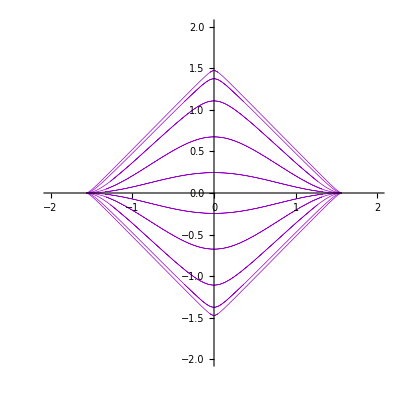

```mathematica
tconst[t_]:=Table[1/2{
+(ArcTan[t-(r-2G μ Log[1+r/(2G μ)])]-ArcTan[t+(r-2G μ Log[1+r/(2G μ)])]),
ArcTan[t-(r-2G μ Log[1+r/(2G μ)])]+ArcTan[t+(r-2G μ Log[1+r/(2G μ)])]},{r,-100,100,0.1}];
tconstP1=Table[tconst[k],{k,{0.25,0.8,2,5,10}}];
tconst[t_]:=Table[1/2{
-(ArcTan[t-(r-2G μ Log[1+r/(2G μ)])]-ArcTan[t+(r-2G μ Log[1+r/(2G μ)])]),
ArcTan[t-(r-2G μ Log[1+r/(2G μ)])]+ArcTan[t+(r-2G μ Log[1+r/(2G μ)])]},{r,-100,100,0.1}];
tconstP2=Table[tconst[k],{k,{0.25,0.8,2,5,10}}]
tconst[t_]:=Table[1/2{
+(ArcTan[t-(r-2G μ Log[1+r/(2G μ)])]-ArcTan[t+(r-2G μ Log[1+r/(2G μ)])]),
-(ArcTan[t-(r-2G μ Log[1+r/(2G μ)])]+ArcTan[t+(r-2G μ Log[1+r/(2G μ)])])},{r,-100,100,0.1}];
tconstP3=Table[tconst[k],{k,{0.25,0.8,2,5,10}}];
tconst[t_]:=Table[1/2{
-(ArcTan[t-(r-2G μ Log[1+r/(2G μ)])]-ArcTan[t+(r-2G μ Log[1+r/(2G μ)])]),
-(ArcTan[t-(r-2G μ Log[1+r/(2G μ)])]+ArcTan[t+(r-2G μ Log[1+r/(2G μ)])])},{r,-100,100,0.1}];
tconstP4=Table[tconst[k],{k,{0.25,0.8,2,5,10}}];
PD2=ListLinePlot[Flatten[{tconstP1,tconstP2,tconstP3,tconstP4},1],PlotRange->{{-2,2},{-2,2}},AspectRatio->1,PlotStyle->{{RGBColor[0.6,0,0.8],AbsoluteThickness[0.5]}}]
```

```mathematica
l=Line[Table[{0.02(-1)^k,-1.52+0.02k},{k,1,150}]];
```

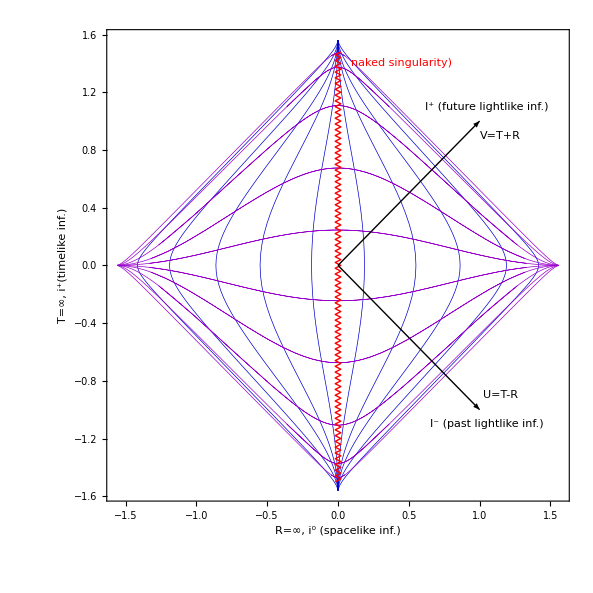

```mathematica
Show[PD1,PD2,Graphics[
{Text["I^+ (future lightlike inf.)",{1.05,1.1}],Text["I^- (past lightlike inf.)",{1.05,-1.1}],
Text["V=T+R",{1.15,0.9}],
Text["U=T-R",{1.15,-0.9}],
Text[Style["naked singularity)",Red],{0.45,1.4}]}],
Graphics[{Red,Thick,l}],
Graphics[Arrow[{{0,0},{1,1}}]],
Graphics[Arrow[{{0,0},{1,-1}}]
]]
```

```mathematica
T=V+U=V+V-R
```

```mathematica
T-R=U
```